```mathematica
e=1.60217663×10^-19;

c= QuantityMagnitude[UnitConvert[Quantity[1, "SpeedOfLight"]]];
mdy = QuantityMagnitude[UnitConvert[Quantity[162,"AtomicMassConstant"]]];
kB = QuantityMagnitude[UnitConvert[Quantity[1,"BoltzmannConstant"]]];
μB = QuantityMagnitude[UnitConvert[Quantity[1,"BohrMagneton"]]];
μ0 = QuantityMagnitude[UnitConvert[Quantity[1,"VacuumPermeability"]]];
ϵ0=1/c^2/μ0;
h=N[QuantityMagnitude[UnitConvert[Quantity[1,"PlanckConstant"]]]];
a0=5.29177*10^-11;

ℏ = h/(2π);
```

156.64

9.24025

156.912

Trap depth is 7.57556 uK.

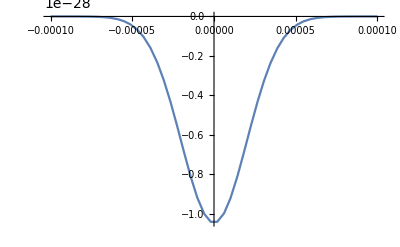

```mathematica
w=40*10^-6 (*um*);
p1=0.25(* watt *);
p2 =0.21(* watt *);
I1[x_,y_,z_]:=2*p1/Pi/w^2*Exp[-2*(x^2+z^2)/w^2]
θ = 5*Pi/180;
I2[x_,y_,z_]:=2*p2/Pi/w^2*Exp[-2*((x*Cos[θ]-y*Sin[θ])^2+z^2)/w^2]
U0[x_,y_,z_]:=-2*Pi*a0^3/c*(I1[x,y,z]+I2[x,y,z])*184;
ωx=Sqrt[(D[U0[x,y,z],{x,2}]/. {x->0,y->0,z->0})/mdy]/(2*Pi)
ωy=Sqrt[(D[U0[x,y,z],{y,2}]/. {x->0,y->0,z->0})/mdy]/(2*Pi)
ωz=Sqrt[(D[U0[x,y,z],{z,2}]/. {x->0,y->0,z->0})/mdy]/(2*Pi)
Print["Trap depth is ",-U0[0,0,0]/kB*10^6," uK."]
Plot[U0[x,0,0],{x,-10^-4,10^-4}]
```

```mathematica
(*Trace the ODT density of our 626 PA try around Sep/Oct 2023, before compress*)
ωho=2*Pi*(90*90*5)^0.3333;
aho=Sqrt[ℏ/mdy/ωho];
a=122*a0;
g=4*Pi*a*ℏ^2/mdy;
Nat=150000;
μ=ℏ*ωho/2*(15*Nat*a/aho)^(2/5);
μ/g
```

1.3909×10^20

```mathematica
(*Trace the ODT density of our 626 PA try around Sep/Oct 2023, after compress*)
Nat =150000;
ωho=2*Pi*(300*300*16)^0.3333;
temp=1.6*10^-6;
Vol=(2*Pi*kB*temp/mdy/ωho^2)^1.5;
Nat/Vol
```

4.56509×10^18

```mathematica
Tf=ℏ*2*Pi*(150*150*10)^0.333*(6*10^4)^0.3333/kB (*111523, fermion try*)
```

1.13765×10^-7